```mathematica
(* Area of an ellipse using "polar coordinates" integration.
https://www.quora.com/How-can-I-find-the-area-enclosed-by-11x-2-4-sqrt-3-xy-7y-2-1-0-via-polar-integration
 *)
eq=11 x^2+4 √3 x y+7 y^2-1==0
```

-1+11 x^2+4 √3 x y+7 y^2==0

```mathematica
fs=Map[#[[2]]&,Solve[eq, y]//Flatten]
```

{1/7 (-2 √3 x-√(7-65 x^2)),1/7 (-2 √3 x+√(7-65 x^2))}

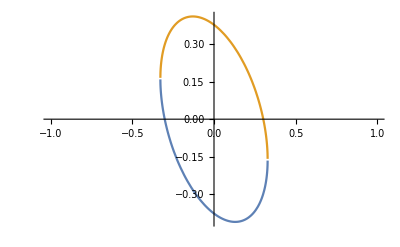

```mathematica
Plot[fs, {x, -1, 1}]
```

```mathematica
p=TransformedField["Cartesian"->"Polar",eq[[1]], {x,y}->{r,θ}]//FullSimplify
```

-1+9 r^2+2 r^2 (Cos[2 θ]+√3 Sin[2 θ])

```mathematica
ps=Map[#[[2]]&,Solve[p==0, r]//Flatten]
```

{-1/(√(9+2 Cos[2 θ]+2 √3 Sin[2 θ])),1/(√(9+2 Cos[2 θ]+2 √3 Sin[2 θ]))}

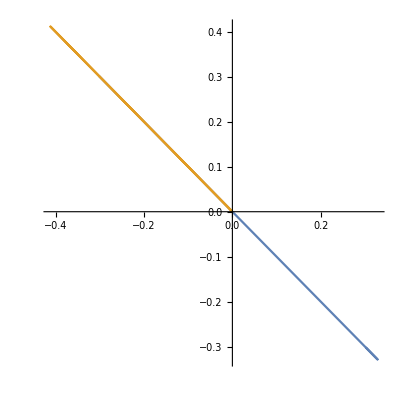

```mathematica
PolarPlot[ps, {θ, 0, π}]
```

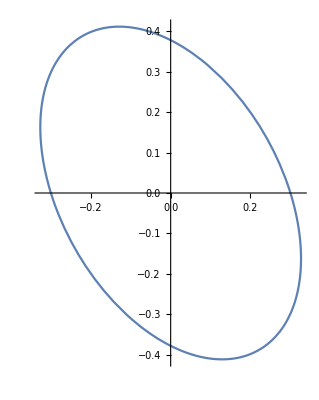

```mathematica
PolarPlot[ps[[2]], {θ, 0, 2π}]
```

```mathematica
ps[[2]]
```

1/(√(9+2 Cos[2 θ]+2 √3 Sin[2 θ]))

```mathematica
(* Jacobian determinant of the mapping between Polar and Cartesian coordinates: *)
𝒥 = ResourceFunction["JacobianDeterminant"][{r Cos[θ],r Sin[θ]},{r,θ}]//Simplify
```

r

```mathematica
∫_0^(2π) ∫_0^ps[[2]] 𝒥 ⅆrⅆθ
```

π/(√65)

```mathematica
(* All at once: *)
Integrate[Integrate[𝒥,{r,0, Solve[TransformedField["Cartesian"->"Polar",11 x^2+4 √3 x y+7 y^2-1, {x,y}->{r,θ}]==0, r][[2]][[1]][[2]]}],{θ,0,2π}]
```

π/(√65)